# Gravity

A bunch of the tools we are looking at were developed to think about planetary motion

Newton’s Laws

For each body F_i=m_i a_i=m_i p''_i
For each planet F_i=C m_i∑_(j=1)^n m_j(p_i-p_j)/(||p_i-p_j(||)^3)

We are going to build the equations and look at some orbits.  We need to decide how we are going to store the positions of all the planets. We need to decide if we are going to solve a first order system or a second order system of half the size.

### Code:

```mathematica
fG[{m1_,p1_},{m2_,p2_}]:= Module[{r=Norm[p1-p2],Tol=10^-12,G=1.0 },
(* in MKS units G=6.67*10^-11 *)
If[r<Tol,0,-G *m1*m2*(p1-p2)/r^3]]

FG[ms_,ps_List]:= Module[{n=Length[ms]},
Table[ 1/ms⟦i⟧Sum[fG[{ms⟦i⟧,ps⟦i⟧},{ms⟦j⟧,ps⟦j⟧}],{j,1,n}],{i,n}]
]
```

Here is a picture of some positions with the gravitational forces.  It is a good idea to check with a picture you have the signs correct.

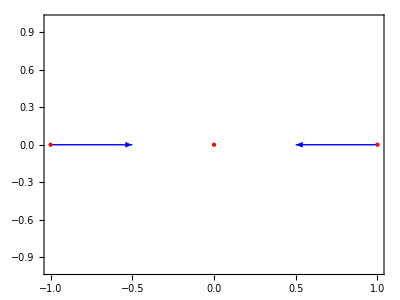

```mathematica
ms={1,1,1};
ps={{-1,0},{0,0},{1,0}};
Fs=FG[ms,ps];
ϵ=0.4;
n=Length[ms];
Graphics[
Table[{
{Blue,Arrow[{ps[[i]],ps[[i]]+ϵ Fs⟦i⟧}]},
{Red,Point[ps⟦i⟧]}
},{i,n}],
Frame->True]
```

## Big Moon: Elliptical Orbit

The earth is about 80 times more massive than the moon. We should probably fix some of the constants in this system!

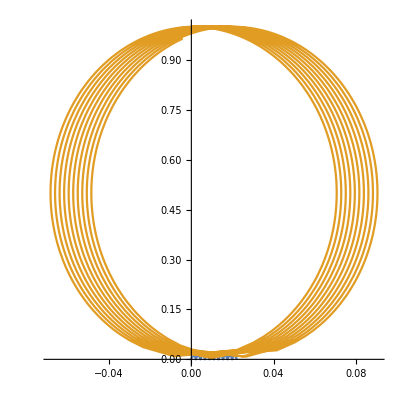

```mathematica
Clear[ps,t]
ms={100,1};
ps0={{0,0},{0,1}};
vs0={{0,0},{1,0}};
TMax=2.2;
pSol=NDSolveValue[ {ps''[t]==FG[ms,ps[t]],ps[0]==ps0,ps'[0]==vs0},ps,{t,0,TMax}];
ParametricPlot[{pSol[t]⟦1⟧,pSol[t]⟦2⟧},{t, 0, TMax},PlotPoints->100,AspectRatio->1,PlotPoints->1234]
```

## Identical Suns: Figure Eight Orbit

Chenciner, Alain, and Richard Montgomery. “A Remarkable Periodic Solution of the Three-Body Problem in the Case of Equal Masses.” Annals of Mathematics, vol. 152, no. 3, 2000, pp. 881–901. JSTOR, https://doi.org/10.2307/2661357. Accessed 27 Oct. 2022.

Figure 1 gives the ICs. 
x1 = −x2 = 0.97000436−0.24308753i,
x3=0; 
x3'=−2 x1=−2 x2=−0.93240737−0.86473146i
T =12T =6.32591398, I(0)=2, m1=m2=m3=1
 Rest of paper is dense!!!!

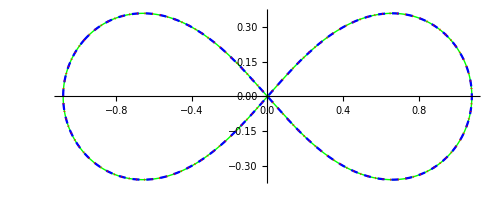

```mathematica
ms={1,1,1};
p10={0.97000436,−0.24308753};
v30={−0.93240737,−0.86473146};
ϵ=0.0;
TMax=6.32591398-ϵ;
ps0={p10,-p10,{0,0}};
vs0={-v30/2,-v30/2,v30};
pSol=NDSolveValue[ {ps''[t]==FG[ms,ps[t]],ps[0]==ps0,ps'[0]==vs0},ps,{t,0,TMax}];
ParametricPlot[{pSol[t]⟦1⟧,pSol[t]⟦2⟧,pSol[t]⟦3⟧},{t, 0, TMax},
PlotStyle->{Directive[Green,Thick],{Blue,Dashed}, {Red,Dotted}}]
```

```mathematica
Pic=ParametricPlot[pSol[t]⟦1⟧,{t, 0, TMax},
PlotStyle->Directive[Green,Thick]];
Manipulate[
Show[Pic, Epilog->Point[pSol[t]]],
{t, 0, TMax}]
```

## Transfer Orbits

Numerical Methods for Differential Equations: A Computational Approach
John R. Dormand, CRC Press, Boca Raton, 1996
E-Book 2017
Question 11/12 p163

Q11: The equations of motion for a space-probe moving in the Earth-Moon system are
	x'' | = |     2y' | + | x | - | (E(x+M))/r_1^3 | - | (M(x-E))/r_2^3
y'' | = | -2x' | + | y | - | (E y)/r_1^3 | - | (M y)/r_2^3 
The Earth is fixed at (-M,0) and the moon is fixed at (E,0) in a rotating coordinate system with period 2π
	M=1/82.45  and E=1-M
and 
	r_1 | = | √((x+M)^2+y^2)
r_2 | = | √((x-E)^2+y^2) 
The very reasonable assumption is that the probe does not perturb the earth moon system.

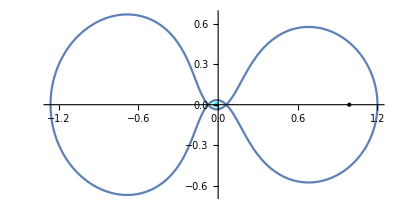

{-2.35545×10^-6,5.87341×10^-6}

```mathematica
Md=1/82.45; Ed=1-Md;
TMax=6.192169331319640;
{xSol,ySol}=NDSolveValue[{
r1[t]=√((x[t]+Md)^2+y[t]^2);
r2[t]=√((x[t]-Ed)^2+y[t]^2);
x''[t]==2y'[t]+x[t]-Ed*(x[t]+Md)/r1[t]^3-Md*(x[t]-Ed)/r2[t]^3,
y''[t]==-2x'[t]+y[t]-Ed*y[t]/r1[t]^3-Md*y[t]/r2[t]^3,
x[0]==1.2,
y[0]==0,
x'[0]==0,
y'[0]==-1.049357509830320
},{x,y},{t, 0, TMax}];
ParametricPlot[{xSol[t],ySol[t]},{t,0, TMax},
Prolog->{{Cyan,PointSize[0.01],Point[{-Md,0}]},Point[{Ed,0}]}]
{xSol[TMax],ySol[TMax]}-{xSol[0],ySol[0]}
```

```mathematica
Rot[t_]:=({{Cos[t], -Sin[t]}, {Sin[t], Cos[t]}}) 
Pic=ParametricPlot[ {Rot[t].{-Md,0},Rot[t].{Ed,0},Rot[t].{xSol[t],ySol[t]}},{t, 0,TMax}];
Manipulate[Show[Pic, 
Epilog->{PointSize[0.02],{Magenta,Point[Rot[t].{0,Ed}]},{Red, Point[Rot[t].{xSol[t],ySol[t]}]}}
],
{t, 0, TMax}]
```

```mathematica
Md=0.012277471; Ed=1-Md;
TMax=29.4602;
{xSol,ySol}=NDSolveValue[{
r1[t]=√((x[t]+Md)^2+y[t]^2);
r2[t]=√((x[t]-Ed)^2+y[t]^2);
x''[t]==2y'[t]+x[t]-Ed*(x[t]+Md)/r1[t]^3-Md*(x[t]-Ed)/r2[t]^3,
y''[t]==-2x'[t]+y[t]-Ed*y[t]/r1[t]^3-Md*y[t]/r2[t]^3,
x[0]==1.15,
y[0]==0,
x'[0]==0,
y'[0]==0.00868829090
},{x,y},{t, 0, TMax}];
ParametricPlot[{xSol[t],ySol[t]},{t,0, TMax},
Prolog->{{Cyan,PointSize[0.01],Point[{-Md,0}]},Point[{Ed,0}]}];
Rot[t_]:=({{Cos[t], -Sin[t]}, {Sin[t], Cos[t]}}) 
Pic=ParametricPlot[ {Rot[t].{-Md,0},Rot[t].{Ed,0},Rot[t].{xSol[t],ySol[t]}},{t, 0,TMax}];
Manipulate[Show[Pic, Epilog->{PointSize[0.03],{Red,Point[Rot[t].{xSol[t],ySol[t]}]},{Black,Point[Rot[t].{Ed,0}]}}],
{t,0, TMax}]
```